```mathematica
Lfull[Lbase_]:=#~Join~{1-Plus@@#}&/@Lbase
```

```mathematica
L3={{0.1666666666666667,0.1666666666666667},{0.6666666666666667,0.1666666666666667},{0.1666666666666667,0.6666666666666667}};w3={0.3333333333333333,0.3333333333333333,0.3333333333333333};
```

```mathematica
L4={{0.3333333333333333,0.3333333333333333},{0.6,0.2},{0.2,0.6},{0.2,0.2}};
w4={-0.5625,0.5208333333333333,0.5208333333333333,0.5208333333333333};
```

```mathematica
L13={{0.333333333333333,0.333333333333333},{0.479308067841923,0.260345966079038},{0.260345966079038,0.479308067841923},{0.260345966079038,0.260345966079038},{0.869739794195598,0.065130102902216},{0.065130102902216,0.869739794195598},{0.065130102902216,0.065130102902216},{0.638444188569809,0.312865496004875},{0.312865496004875,0.638444188569809},{0.638444188569809,0.048690315425316},{0.048690315425316,0.638444188569809},{0.312865496004875,0.048690315425316},{0.048690315425316,0.312865496004875}};
w13={-0.149570044467670,0.175615257433204,0.175615257433204,0.175615257433204,0.053347235608839,0.053347235608839,0.053347235608839,0.077113760890257,0.077113760890257,0.077113760890257,0.077113760890257,0.077113760890257,0.077113760890257};
```

```mathematica
pts={{h,0,0},{0,2h,0},{0,0,3h}}
```

{{h,0,0},{0,2 h,0},{0,0,3 h}}

```mathematica
monoms[n_]:=Cases[Flatten@Table[If[α+β+γ==n&&α>=β>=γ,x^α y^β z^γ],{α,0,n},{β,0,n},{γ,0,n}],Except[Null]]
```

```mathematica
fo[n_]:=Function[{r},#/.{x->r[[1]],y->r[[2]],z->r[[3]]}]&/@monoms[n]
```

```mathematica
IG[f_,L_,w_,pts_]:=Area[Triangle[pts]]Sum[w[[i]]f[L[[i]][[1]]pts[[1]]+L[[i]][[2]]pts[[2]]+L[[i]][[3]]pts[[3]]],{i,Length@L}]
IGhalf[f_,L_,w_,pts_]:=Area[Triangle[pts]]/4(Sum[w[[i]](f[L[[i]][[1]]pts[[1]]+L[[i]][[2]](pts[[2]]+pts[[1]])/2+L[[i]][[3]](pts[[3]]+pts[[1]])/2]+f[L[[i]][[1]]pts[[2]]+L[[i]][[2]](pts[[2]]+pts[[3]])/2+L[[i]][[3]](pts[[2]]+pts[[1]])/2]+f[L[[i]][[1]]pts[[3]]+L[[i]][[2]](pts[[3]]+pts[[1]])/2+L[[i]][[3]](pts[[3]]+pts[[2]])/2]+f[L[[i]][[1]](pts[[1]]+pts[[2]])/2+L[[i]][[2]](pts[[1]]+pts[[3]])/2+L[[i]][[3]](pts[[2]]+pts[[3]])/2]),{i,Length@L}])
IE[f_,pts_]:=Integrate[f[{x,y,z}],{x,y,z}∈Triangle[pts]]
```

{-5.55112×10^-17,-0.0311111,0.0155556,-0.0155556}

{-8.32667×10^-17,-0.00194444,0.000972222,-0.000972222}

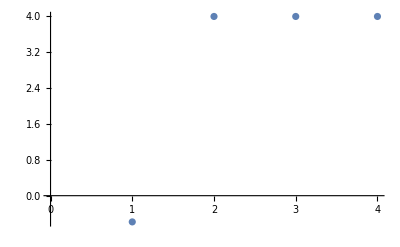

```mathematica
ord=4;
monoms[ord];
ig=IG[#,Lfull@L4,w4,pts/.h->1]&/@fo[ord];
ighalf=IGhalf[#,Lfull@L4,w4,pts/.h->1]&/@fo[ord];
ie=(IE[#,pts/.h->1]&/@fo[ord])//N;
r1=ig-ie
r2=ighalf-ie
ListPlot[Log[2,r1/r2]]
```